```mathematica
bestFitTransform[A_,B_]:=Module[{m,centroidA,centroidB,AA,BB,H,U,S,Vt,R,t,T},(*Get number of dimensions*)
m=Dimensions[A][[2]];

(*Translate points to their centroids*)
centroidA=Mean[A];
centroidB=Mean[B];
AA=A-Table[centroidA,{Length[A]}];
BB=B-Table[centroidB,{Length[B]}];

(*Rotation matrix*)
H=Transpose[AA].BB;
{U,S,Vt}=SingularValueDecomposition[H];
R=Vt.Transpose[U];

(*Special reflection case*)
If[Det[R]<0,Vt[[m]]*=-1;R=Vt.Transpose[U]];

(*Translation*)
t=Flatten[Transpose[{centroidB}]-R.Transpose[{centroidA}]];

(*Homogeneous transformation*)
T=IdentityMatrix[m+1];
T[[1;;m,1;;m]]=R;
T[[1;;m,-1]]=t;

{T,R,t}//Chop
]
```

```mathematica
nearestNeighbor[src_,dst_]:=Module[{neigh,dstpoints,indices},

(*For each point in src, find the closest point in dst*)
neigh=Nearest[dst];
dstpoints=Transpose[neigh[src]][[1]];

(*Find the indices of the dstpoints points*)
indices=Table[Position[dst,dstpoints[[i]]][[1]][[1]],{i,1,Dimensions[dstpoints][[1]]}];

{dstpoints,indices}
]
```

Example on how to use the bestFitTransform function:

```mathematica
Amat=Table[{t,Sin[t]},{t,0,2π,0.1}];
rot=RotationTransform[π/2];
Bmat=rot[Amat];
```

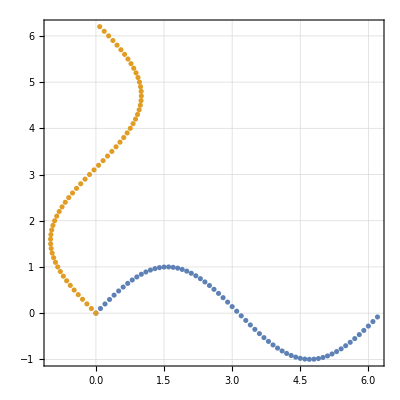

```mathematica
ListPlot[{Amat,Bmat},AspectRatio->1,Frame->True,GridLines->Automatic]
```

```mathematica
{myT,myR,myt}=bestFitTransform[Amat,Bmat]
```

{{{0,-1.,0},{1.,0,0},{0,0,1}},{{0,-1.},{1.,0}},{0,0}}

Example on how to use the nearestNeighbor function

```mathematica
src={{1,0},{2,0},{3,0}}
dst={{1,2},{5,0}}
```

{{1,0},{2,0},{3,0}}

{{1,2},{5,0}}

```mathematica
nearestNeighbor[src,dst]
```

{{{1,2},{1,2},{5,0}},{1,1,2}}

```mathematica
icp[A_,B_,maxIterations_: 20]:=Module[{src,dst,distances,indices,T,R,t},

src=A;
dst=B;

Do[
indices=nearestNeighbor[src,dst][[2]];

{T,R,t}=bestFitTransform[src,dst[[indices]]];
src=Transpose[R.Transpose[src]+t];

,{i,maxIterations}];

src
]
```

```mathematica
newB=icp[A,B];
```

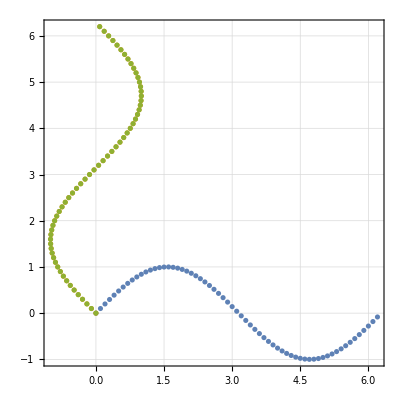

```mathematica
ListPlot[{A,B,newB},AspectRatio->1,Frame->True,GridLines->Automatic]
```

```mathematica
figs=Table[ListPlot[{A,B,icp[A,B,i]},AspectRatio->1,Frame->True,GridLines->Automatic,PlotRange->{{-3.5,6.5},{-2,6.5}}],{i,0,20}];
```

```mathematica
Manipulate[figs[[i]],{i,1,20,1}]
```